# HW6

```mathematica
shahaf zohar - 205978000
Roey Salah -206115438
```

## Assignment 6-Core-Periphery

Compute the Core - Periphery partition "Network of Thrones"

with and without weights (nodes degree is the sum of weights)

You need to

1. Generate the power shift diagram (according to degree (weighted and unweighted)

2. Generate the Core graph.What is the size of the core?Who is in the core?

3. Generate the Periphery graph.What is the size of the core?

4. Generate the matrix and show the symmetry point

Compare the results to a shift diagram of random order of nodes and to a shift diagram with random configuration model of the same degree sequence

Bonus:Do the same but with your favorite centrality measure

#### Load the network with and without weigths

```mathematica
SetDirectory[NotebookDirectory[]];
file=Rest[Import["stormofswords.csv"]];
tribes=Import["tribes.csv"];
nodes=Flatten[tribes⟦All,1⟧];
nodesTribe=Flatten[tribes[[All,2]]];
edges=#⟦1⟧<->#⟦2⟧&/@file[[All,{1,2}]];
GraphTWight=Graph[nodes,edges,EdgeWeight->file⟦All,3⟧];
GraphT=Graph[nodes,edges];
```

#### functions

```mathematica
Rich[G_,k_,deg_]:=VertexList[G][[Ordering[deg,k,Greater]]]
SymmetryPointSize[G_,deg_] :=First@First@Position[Accumulate[deg],Select[Accumulate[deg],#≥ Total[deg]/2&,1][[1]]]
RenameGraphN[g_, sl_]:=Module[{G= g,VrDg = sl,VrLs,VrLst,SVrLst,NewName,edges,NewEdges, ed},
VrLs =VertexList[G];
VrLst = Table[{VrDg[[i]], VrLs[[i]]},{i,Length[VrDg]}];
SVrLst= Sort[VrLst,#1[[1]]>#2[[1]]&];
NewName = Table[SVrLst[[i]][[2]],{i,Length[VrDg]}];
edges = EdgeList[G];
If[DirectedGraphQ[G], 
NewEdges =Table[Position[NewName,edges[[i]][[1]]][[1]][[1]]->Position[NewName,edges[[i]][[2]]][[1]][[1]],{i,Length[edges]}],
NewEdges =Table[Position[NewName,edges[[i]][[1]]][[1]][[1]]<->Position[NewName,edges[[i]][[2]]][[1]][[1]],{i,Length[edges]}]];
{ NewName,Table[SVrLst[[i]][[1]],{i,Length[VrDg]}],
Graph[Range[Length[VrLst]],NewEdges]}]

SymmetryPoint[G_,M_]:=Module[{s,EE={}, EP={}, PE={},PP={},ee=0,ep=0, pe=0,pp=0,tc, bc, tr,br},
s=Length[VertexList[G]];
ee = M[[1]][[1]];
pe = Total[Total[Take[M,{2,s},{1,1}]]];
ep = Total[Total[Take[M,{1,1},{2,s}]]];
pp = Total[Total[Take[M,{2,s},{2,s}]]];
EE= {0,ee/2};
EP ={0,ep/2};
PE= {0,pe/2};
PP= {EdgeCount[G],pp/2};
For[i=1,i < s-1,i++;
tc = Total[Total[Take[M,{1,i-1},{i,i}]]];
bc = Total[Total[Take[M,{i+1,s},{i,i}]]];
tr = Total[Total[Take[M,{i,i},{1,i-1}]]];
br = Total[Total[Take[M,{i,i},{i+1,s}]]];
ee = ee + tc + tr+M[[i]][[i]];
ep =ep + br -tc;
pe = pe + bc -tr;
pp = pp - bc - br-M[[i]][[i]];;
EE =Join[EE,{ee/2}];
EP = Join[EP, {ep/2}];
PE = Join[PE,{pe/2}];
PP = Join[PP, {pp/2}];];
{EE,EP+PE, PP}]
```

```mathematica
(*calculate for weigth graph the "degree" as the sum of weigths*)
(*Compute the weighted adjacency matrix*)
UnWight=AdjacencyMatrix[GraphT];
WightT=Normal[WeightedAdjacencyMatrix[GraphTWight]];
(*Compute the degree of each vertex using the weighted adjacency matrix*)
degreesW = Total/@WightT;
degrees=Total/@UnWight;
```

```mathematica
namelistcoreW =VertexList[GraphTWight];
namelistcore =VertexList[GraphT];
resW=RenameGraphN[GraphTWight,degreesW];
res=RenameGraphN[GraphT,VertexDegree[GraphT]];
sortDegW=resW[[2]];
namelistSortW=resW[[1]];
DegreeOrderGraphW =resW[[3]];
sortDeg=res[[2]];
namelistSort=res[[1]];
DegreeOrderGraph =res[[3]];
```

### plot with weigths

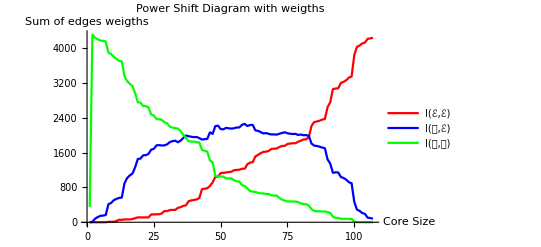

```mathematica
ListLinePlot[SymmetryPoint[RenameGraphN[GraphTWight,degreesW][[3]],WightT],PlotLegends->{"I(ℰ,ℰ)","I(𝒫,ℰ)","I(𝒫,𝒫)"},PlotRange->All,AxesLabel->{"Core Size","Sum of edges weigths"},PlotLabel->"Power Shift Diagram with weigths",PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}}]
```

### plot without weigths

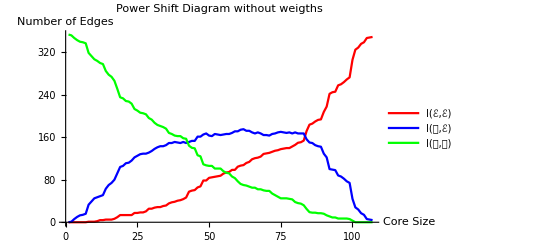

```mathematica
ListLinePlot[SymmetryPoint[RenameGraphN[GraphT,VertexDegree[GraphT]][[3]],UnWight],PlotLegends->{"I(ℰ,ℰ)","I(𝒫,ℰ)","I(𝒫,𝒫)"},PlotRange->All,AxesLabel->{"Core Size","Number of Edges"},PlotLabel->"Power Shift Diagram without weigths",PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}}]
```

#### Core graph

Core graph whit Wight

```mathematica
Rich[GraphTWight,SymmetryPointSize[DegreeOrderGraphW,Flatten[sortDegW]],degreesW]
```

{Tyrion,Jon,Sansa,Jaime,Bran,Robb,Samwell,Arya,Joffrey,Daenerys,Cersei,Tywin,Catelyn,Hodor,Mance}

#### before

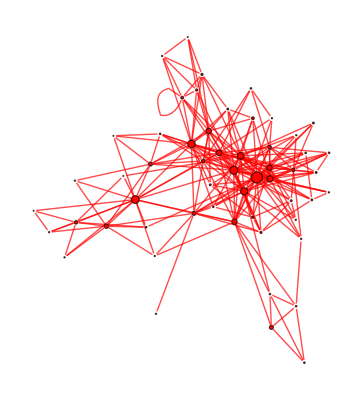

234

55

```mathematica
CoreWbefore=Subgraph[GraphTWight,Rich[GraphTWight,SymmetryPointSize[DegreeOrderGraph,VertexDegree[GraphTWight]],VertexDegree[GraphTWight]],VertexLabels->Table[VertexList[GraphTWight][[i]]->Placed[VertexList[GraphTWight][[i]],Tooltip],{i,1,VertexCount[GraphTWight]}],VertexSize->Thread[VertexList[GraphTWight]->Rescale[VertexDegree[GraphTWight]]],VertexStyle->Red,EdgeStyle->Red]
EdgeCount[CoreWbefore]
VertexCount[CoreWbefore]
```

### After

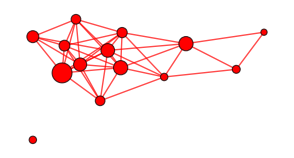

{Tyrion,Jon,Sansa,Jaime,Bran,Robb,Samwell,Arya,Joffrey,Daenerys,Cersei,Tywin,Catelyn,Hodor,Mance}

42

14

```mathematica
CoreW=Subgraph[CoreWbefore,Rich[GraphTWight,SymmetryPointSize[DegreeOrderGraphW,Flatten[sortDegW]],degreesW]]
Rich[GraphTWight,SymmetryPointSize[DegreeOrderGraphW,Flatten[sortDegW]],degreesW]
EdgeCount[CoreW]
VertexCount[CoreW]
```

### Core graph

Core graph without Wight

```mathematica
Rich[GraphT,SymmetryPointSize[DegreeOrderGraph,Flatten[sortDeg]],degrees]
```

{Tyrion,Sansa,Jon,Robb,Jaime,Tywin,Cersei,Arya,Robert,Joffrey,Catelyn,Samwell,Stannis,Daenerys,Bran,Sandor,Mance,Gregor,Eddard}

### before

```mathematica
Corebefore=Subgraph[GraphT,Rich[GraphT,SymmetryPointSize[DegreeOrderGraph,VertexDegree[GraphT]],VertexDegree[GraphT]],VertexLabels->Table[VertexList[GraphTWight][[i]]->Placed[VertexList[GraphT][[i]],Tooltip],{i,1,VertexCount[GraphT]}],VertexSize->Thread[VertexList[GraphTWight]->Rescale[VertexDegree[GraphT]]],VertexStyle->Red,EdgeStyle->Red]
EdgeCount[Corebefore]
VertexCount[Corebefore]
```

-Graphics-

234

55

### After

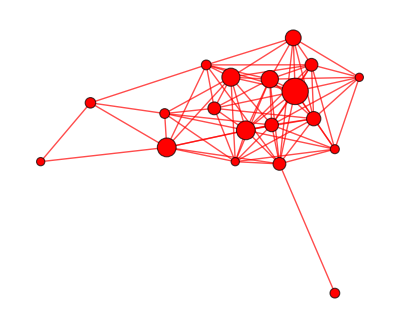

{Tyrion,Sansa,Jon,Robb,Jaime,Tywin,Cersei,Arya,Robert,Joffrey,Catelyn,Samwell,Stannis,Daenerys,Bran,Sandor,Mance,Gregor,Eddard}

82

19

```mathematica
Core=Subgraph[Corebefore,Rich[GraphT,SymmetryPointSize[DegreeOrderGraph,Flatten[sortDeg]],degrees]]
Rich[GraphT,SymmetryPointSize[DegreeOrderGraph,Flatten[sortDeg]],degrees]
EdgeCount[Core]
VertexCount[Core]
```

#### Periphery graph

graph whit Wight

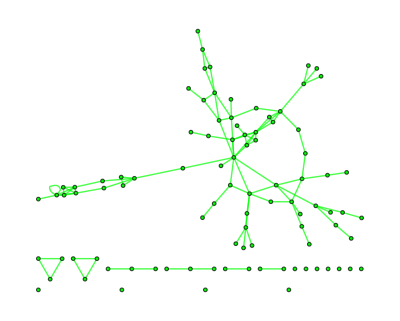

93

106

```mathematica
PeripW=Subgraph[GraphTWight,Complement[VertexList[GraphTWight],VertexList[CoreW]],VertexStyle->Green,EdgeStyle->Green]
VertexCount[PeripW]
EdgeCount[PeripW]
```

Without weigths

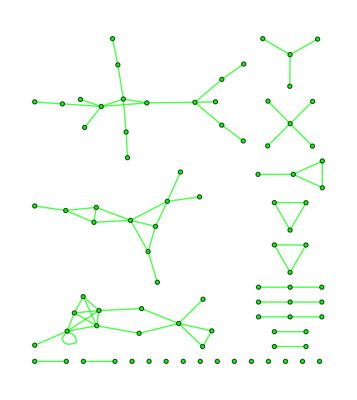

88

77

```mathematica
Perip=Subgraph[GraphT,Complement[VertexList[GraphT],VertexList[Core]],VertexStyle->Green,EdgeStyle->Green]
VertexCount[Perip]
EdgeCount[Perip]
```

### Putting it Together

With weigths

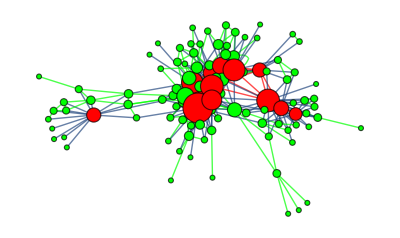

```mathematica
HighlightGraph[GraphTWight,{Style[VertexList[CoreW],Red],Style[VertexList[PeripW],Green],Style[EdgeList[CoreW],Red],Style[EdgeList[PeripW],Green]},VertexSize->Thread[VertexList[GraphTWight]->1+5*Rescale[VertexDegree[GraphTWight]]]]
```

Without weigths

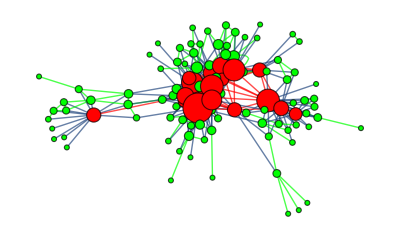

```mathematica
HighlightGraph[GraphT,{Style[VertexList[Core],Red],Style[VertexList[Perip],Green],Style[EdgeList[Core],Red],Style[EdgeList[Perip],Green]},VertexSize->Thread[VertexList[GraphT]->1+5*Rescale[VertexDegree[GraphT]]]]
```

#### Matrix with symmetry point

With weigths

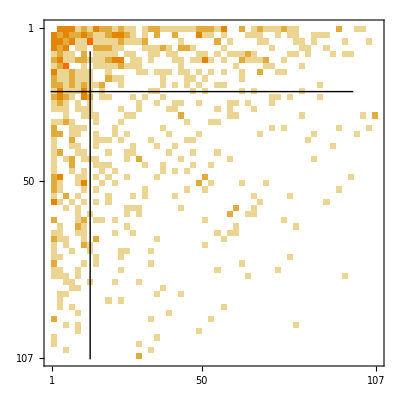

```mathematica
CoreRatioW= VertexCount[CoreW]/VertexCount[GraphTWight];
Show[MatrixPlot[AdjacencyMatrix[DegreeOrderGraphW]],Graphics[{{Thick,Line[{{CoreRatioW*50,0},{CoreRatioW*50,50}}]},{Thick,Line[{{0,50-CoreRatioW*50},{50,50-CoreRatioW*50}}]}}]]
```

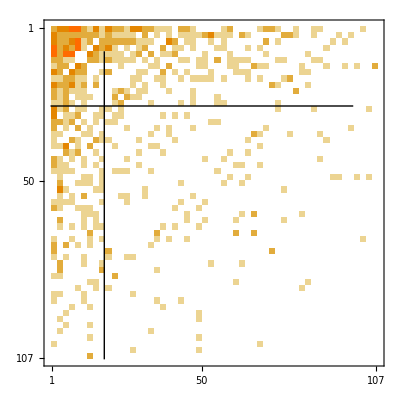

```mathematica
CoreRatio= VertexCount[Core]/VertexCount[GraphT];
Show[MatrixPlot[AdjacencyMatrix[DegreeOrderGraph]],Graphics[{{Thick,Line[{{CoreRatio*50,0},{CoreRatio*50,50}}]},{Thick,Line[{{0,50-CoreRatio*50},{50,50-CoreRatio*50}}]}}]]
```

#### compare result to shift diagram of random order of nodes and to random configuration model

Random order

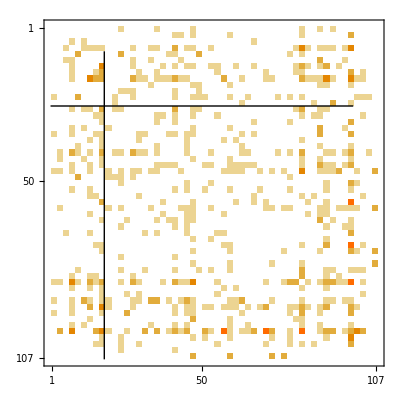

```mathematica
DegreeOutput=Map[VertexDegree[GraphT,#]&,RandomOrderGraph];
resRand=RenameGraphN[GraphT,RandomOrderGraph,DegreeOutput];
RandomOrderGraph= resRand[[1]];
Show[MatrixPlot[AdjacencyMatrix[RandomOrderGraph]],Graphics[{{Thick,Line[{{CoreRatio*50,0},{CoreRatio*50,50}}]},{Thick,Line[{{0,50-CoreRatio*50},{50,50-CoreRatio*50}}]}}]]
```

configuration model

```mathematica
DegreeOutput=Map[VertexDegree[GraphT,#]&,RandomOrderGraph];
resRand=RenameGraphN[GraphT,RandomOrderGraph,DegreeOutput];
RandomOrderGraph= resRand[[1]];
Show[MatrixPlot[AdjacencyMatrix[RandomOrderGraph]],Graphics[{{Thick,Line[{{CoreRatio*50,0},{CoreRatio*50,50}}]},{Thick,Line[{{0,50-CoreRatio*50},{50,50-CoreRatio*50}}]}}]]
```

-Graphics-